```mathematica
Adj={{0,1,1,1,1,0,0,0,1,0},{1,0,1,1,0,1,0,0,0,0},{1,1,0,1,0,0,1,0,0,0},{1,1,1,0,0,0,0,1,0,0},{1,0,0,0,0,0,1,1,0,0},{0,1,0,0,0,0,1,1,0,0},{0,0,1,0,1,1,0,1,0,0},{0,0,0,1,1,1,1,0,0,1},{1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0}}
```

{{0,1,1,1,1,0,0,0,1,0},{1,0,1,1,0,1,0,0,0,0},{1,1,0,1,0,0,1,0,0,0},{1,1,1,0,0,0,0,1,0,0},{1,0,0,0,0,0,1,1,0,0},{0,1,0,0,0,0,1,1,0,0},{0,0,1,0,1,1,0,1,0,0},{0,0,0,1,1,1,1,0,0,1},{1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0}}

AdjacencyMatrix::graph: A graph object is expected at position 1 in AdjacencyMatrix[{{0,1,1,1,1,0,0,0,1,0},{1,0,1,1,0,1,0,0,0,0},{1,1,0,1,0,0,1,0,0,0},{1,1,1,0,0,0,0,1,0,0},{1,0,0,0,0,0,1,1,0,0},{0,1,0,0,0,0,1,1,0,0},{0,0,1,0,1,1,0,1,0,0},{0,0,0,1,1,1,1,0,0,1},{1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0}}].

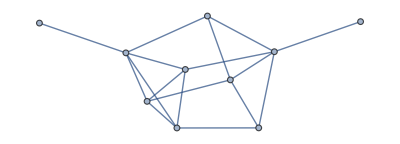

```mathematica
AdjacencyGraph[Adj]
```

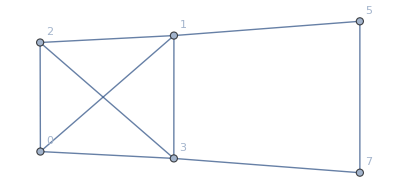

SparseArray[…]

```mathematica
edges={0<->1,0<->2,0<->3,1<->2,1<->3,2<->3,4<->6,4<->7,5<->6,5<->7,6<->7,0<->4,1<->5,2<->6,3<->7,8<->0,9<->7};

(*Create the graph*)
graph=Graph[edges,VertexLabels->"Name"];

(*Delete nodes 8,9,6,and 4*)
modifiedGraph=VertexDelete[graph,{8,9,6,4}];

(*Display the modified graph*)
modifiedGraph
Adjmodified=AdjacencyMatrix[modifiedGraph]
```

```mathematica
TableForm[%74]
```

0 | 1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0

```mathematica
MatrixForm[Adjmodified]
```

(0 | 1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0)

```mathematica
SigmaQInvFun[Adj_]:=ArrayFlatten[{{IdentityMatrix[Length[Adj]],-Adj},{-Adj,IdentityMatrix[Length[Adj]]}}]
SigmaQFun[Adj_]:=Inverse[SigmaQInvFun[Adj]]
NormHafn[c_,gamma_]:=Exp[-1/2*gamma^2*Total[SigmaQFun[c*Adjmodified],2]]/(Sqrt[Det[SigmaQFun[c*Adjmodified]]])
HafnSquared[c_,gamma_]:=(3c^2+6gamma^2c+gamma^4)^2
ProbMaxClique[c_,gamma_]:=Exp[-1/2*gamma^2*Total[SigmaQFun[c*Adjmodified],2]]/(Sqrt[Det[SigmaQFun[c*Adjmodified]]])*(3c^2+6gamma^2c+gamma^4)^2
ProbMaxClique[0.1,1]
```

0.000421673

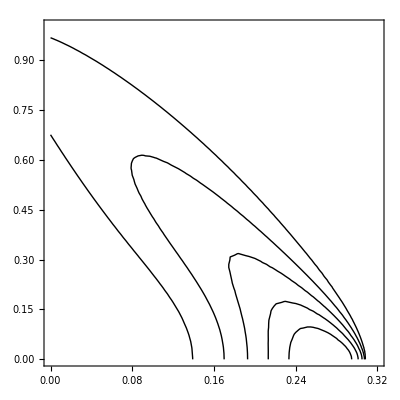

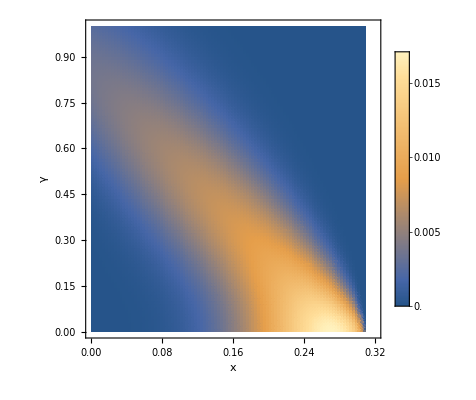

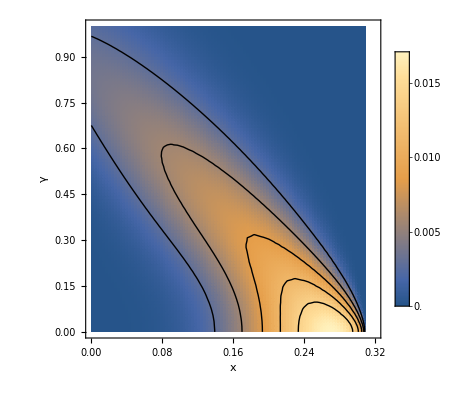

```mathematica
contourPlot=ContourPlot[ProbMaxClique[c,gamma],{c,0,0.32},{gamma,0,1},ContourStyle->Black,Contours->5,ContourShading->None ]
densityPlot=DensityPlot[ProbMaxClique[c,gamma],{c,0,0.32},{gamma,0,1},AxesLabel->{"x",Style["γ",FontSize->32,Italic,Red]},PlotRange->Full,PlotPoints->100,Frame->True,FrameLabel->{"x","γ"},TicksStyle->Directive[FontSize->20],PlotLegends->Automatic]

Show[densityPlot,contourPlot]
```

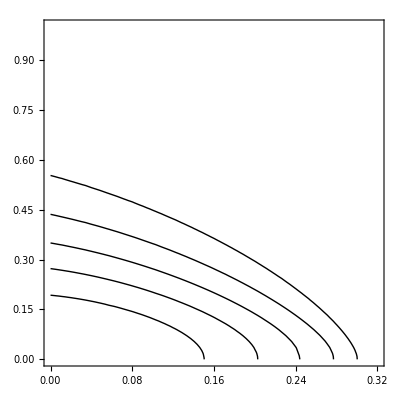

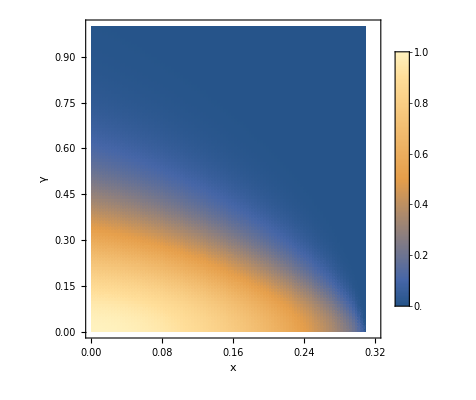

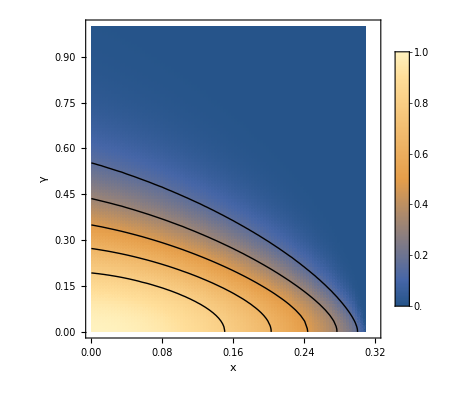

```mathematica
contourPlot=ContourPlot[NormHafn[c,gamma],{c,0,0.32},{gamma,0,1},ContourStyle->Black,Contours->5,ContourShading->None ]
densityPlot=DensityPlot[NormHafn[c,gamma],{c,0,0.32},{gamma,0,1},AxesLabel->{"x",Style["γ",FontSize->32,Italic,Red]},PlotRange->Full,PlotPoints->100,Frame->True,FrameLabel->{"x","γ"},TicksStyle->Directive[FontSize->20],PlotLegends->Automatic]

Show[densityPlot,contourPlot]
```

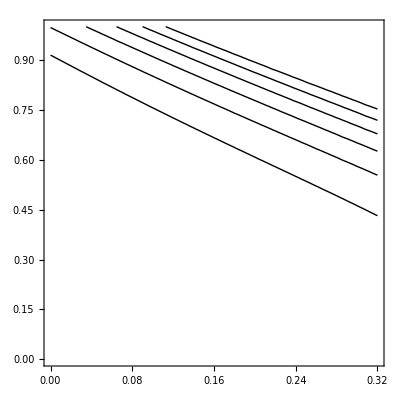

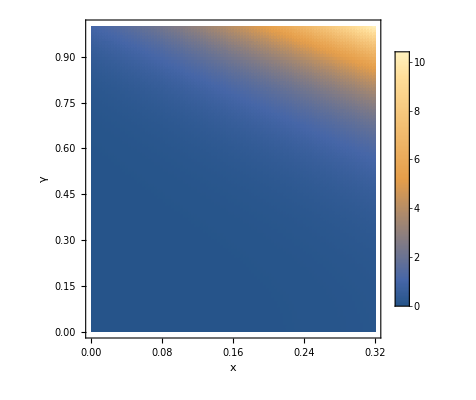

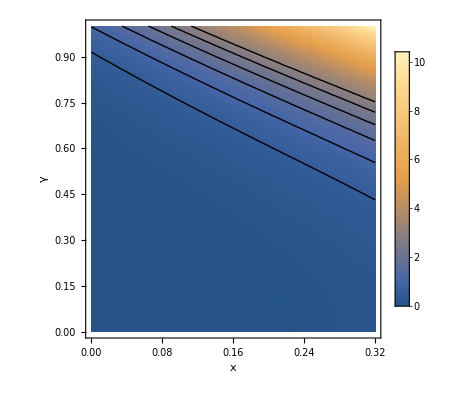

```mathematica
contourPlot=ContourPlot[HafnSquared[c,gamma],{c,0,0.32},{gamma,0,1},ContourStyle->Black,Contours->6,ContourShading->None ]
densityPlot=DensityPlot[HafnSquared[c,gamma],{c,0,0.32},{gamma,0,1},AxesLabel->{"x",Style["γ",FontSize->32,Italic,Red]},PlotRange->Full,PlotPoints->100,Frame->True,FrameLabel->{"x","γ"},TicksStyle->Directive[FontSize->20],PlotLegends->Automatic]

Show[densityPlot,contourPlot]
```